# Asynchronous motor simulation

## Clockwise rotation

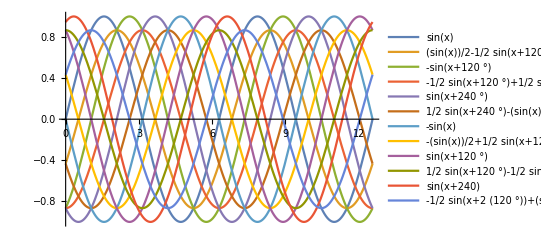

```mathematica
Plot[{Sin [x],Sin[x]/2-Sin[x+120Degree]/2,-Sin [x+120Degree],-Sin[x+120Degree]/2+Sin[x+240Degree]/2,Sin[x+240Degree],Sin[x+240Degree]/2-Sin[x]/2,-Sin[x],-Sin[x]/2+Sin[x+120Degree]/2,Sin[x+120Degree],Sin[x+120Degree]/2-Sin[x+2*(120Degree)]/2,Sin[x+240],-Sin[x+2*(120Degree)]/2+Sin[x]/2},{x,0,4Pi}, PlotLegends->"Expressions"]
```

```mathematica
v=(*sebesség*)
F[m_,a_]:= m*a
V=a*t
a=v/t
V.ERR = V.CURR - V.TAR
F.BRK = D.BRK * V.ERR (* P.BRK open loop*)
F.ENG = D.ENG * V.ERR  (* P.ENG open loop*)
```

SetDelayed::write: Tag Times in (a m)[m_,a_] is Protected.

$Failed

a t

a

Set::write: Tag Dot in V.ERR is Protected.

V.CURR-V.TAR

Set::write: Tag Dot in (a m).BRK is Protected.

D.BRK V.ERR

Set::write: Tag Dot in (a m).ENG is Protected.

D.ENG V.ERR

```mathematica
Manipulate[Grid[{{Plot[a2 Sin[n2 (x+p2)],{x,0,2 Pi},AspectRatio->1,PlotRange->1],ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"]},{Null,ParametricPlot[{a1 Sin[n1 (x+p1)],x},{x,0,2 Pi},AspectRatio->1,PlotRange->{{-1,1},{0,2 Pi}}]}}],{{n1,1,"Frequency"},1,4},{{a1,1,"Amplitude"},0,1},{{p1,0,"Phase"},0,2 Pi},Delimiter,{{n2,5/4,"Frequency"},1,4},{{a2,1,"Amplitude"},0,1},{{p2,0,"Phase"},0,2 Pi},ControlPlacement->Left]
```

{{y[x]→ⅇ^(-x/2) C[2] Cos[(√3 x)/2]+ⅇ^(-x/2) C[1] Sin[(√3 x)/2]}}

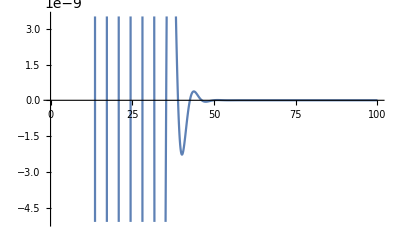

```mathematica
sol=DSolve[y''[x]+y'[x]+y[x]==0,y[x],x]

Plot[{y[x]/.sol/.{C[1]->1,C[2]->1}},{x,10,100},PlotRange->Automatic]
```

```mathematica
{{y->Function[{x},1/3 (3 Cos[x]+Sin[x])]}}

Manipulate[DSolve[{v''[t]+2*Deng*v[t]+Keng/(2*Mveh)*Keng/(2*Mveh)*v[t]==0,v[0]==0,v'[0]==0,v''[0]=0},v,t],Grid[{{Plot[Evaluate[y[x]/.%/.{{a->1/13},{a->1/2},{a->4}}],{x,0,18}],Plot[Evaluate[y[x]/.%/.{{a->1/13},{a->1/2},{a->4}}],{x,0,18}]}}],{{t,0},0,100},{Vtar,0,3.7},{{Vcur,0},0,3.7},{{Mveh,1200},1000,2000,10},{{Dbrk,10},1,100},{{Deng,10},1,100},{{Keng,1},0,10},{{Kbrk,1},0,10},ContentSize->{1000, 1000}]
```

{{y→Function[{x},1/3 (3 Cos[x]+Sin[x])]}}

DSolve::dsvar: 0 cannot be used as a variable.

```mathematica
Manipulate[Grid[{Plot[Evaluate[y[x]/.%/.{{a->1/13},{a->1/2},{a->4}}],{x,0,18}],Plot[d,{d,0,t},PlotRange->{{-1,13}}]}],{t,1,100},{Vtar,0,3.7},{{Vcur,0},0,3.7},{{Mveh,1200},1000,2000,10},{{Dbrk,10},1,100},{{Deng,10},1,100},ContentSize->{1000, 1000}]
```

ReplaceAll::reps: {} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Manipulate::vsform: Manipulate argument {1,1,100} does not have the correct form for a variable specification.

Manipulate::vsform: Manipulate argument {0,0,3.7} does not have the correct form for a variable specification.

Manipulate::vsform: Manipulate argument {{0,0},0,3.7} does not have the correct form for a variable specification.

General::stop: Further output of Manipulate::vsform will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Manipulate::vsform: Manipulate argument {1,1,100} does not have the correct form for a variable specification.

Manipulate::vsform: Manipulate argument {0,0,3.7} does not have the correct form for a variable specification.

Manipulate::vsform: Manipulate argument {{0,0},0,3.7} does not have the correct form for a variable specification.

General::stop: Further output of Manipulate::vsform will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Manipulate::vsform: Manipulate argument {1,1,100} does not have the correct form for a variable specification.

Manipulate::vsform: Manipulate argument {0,0,3.7} does not have the correct form for a variable specification.

Manipulate::vsform: Manipulate argument {{0,0},0,3.7} does not have the correct form for a variable specification.

General::stop: Further output of Manipulate::vsform will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Manipulate[Graphics[{Red,Thick,Line[{
{{1,0},{1,Sin[x]}},
{{2,0},{2,Sin[x]/2-Sin[x+120Degree]/2}},
{{3,0},{3,-Sin[x+120Degree]}},
{{4,0},{4,-Sin[x+120Degree]/2+Sin[x+240Degree]/2}},
{{5,0},{5,Sin[x+240Degree]}},
{{6,0},{6,Sin[x+240Degree]/2-Sin[x]/2}},
{{7,0},{7,-Sin[x]}},
{{8,0},{8,-Sin[x]/2+Sin[x+120Degree]/2}},
{{9,0},{9,Sin[x+120Degree]}},
{{10,0},{10,Sin[x+120Degree]/2-Sin[x+2*(120Degree)]/2}},
{{11,0},{11,Sin[x+240]}},
{{12,0},{12,-Sin[x+2*(120Degree)]/2+Sin[x]/2}}
}]},Axes->True,GridLines->Automatic,PlotRange->{{-1,13},{-2,2}}],{t,0,100}]
```

```mathematica
Manipulate[Graphics[{Red,Thick,Circle[{0,0},10],Blue,
Circle[{Sin[345Degree]*10,Cos[345Degree]*10},1],
Line[{{Sin[45Degree]*0.5+Sin[345Degree]*10,Cos[45Degree]*0.5+Cos[345Degree]*10},{Sin[45Degree]*-0.5+Sin[345Degree]*10,Cos[45Degree]*-0.5+Cos[345Degree]*10}}],
Line[{{Sin[45Degree]*0.5+Sin[345Degree]*10,Cos[45Degree]*-0.5+Cos[345Degree]*10},{Sin[45Degree]*-0.5+Sin[345Degree]*10,Cos[45Degree]*0.5+Cos[345Degree]*10}}],
Circle[{Sin[15Degree]*10,Cos[15Degree]*10},1],
Line[{{Sin[45Degree]*0.5+Sin[15Degree]*10,Cos[45Degree]*0.5+Cos[15Degree]*10},{Sin[45Degree]*-0.5+Sin[15Degree]*10,Cos[45Degree]*-0.5+Cos[15Degree]*10}}],
Line[{{Sin[45Degree]*0.5+Sin[15Degree]*10,Cos[45Degree]*-0.5+Cos[15Degree]*10},{Sin[45Degree]*-0.5+Sin[15Degree]*10,Cos[45Degree]*0.5+Cos[15Degree]*10}}],Black,
Circle[{Sin[45Degree]*10,Cos[45Degree]*10},1],
Disk[{Sin[45Degree]*10,Cos[45Degree]*10},0.5],
Circle[{Sin[75Degree]*10,Cos[75Degree]*10},1],
Disk[{Sin[75Degree]*10,Cos[75Degree]*10},0.5],Green,
Circle[{Sin[105Degree]*10,Cos[105Degree]*10},1],
Line[{{Sin[45Degree]*0.5+Sin[105Degree]*10,Cos[45Degree]*0.5+Cos[105Degree]*10},{Sin[45Degree]*-0.5+Sin[105Degree]*10,Cos[45Degree]*-0.5+Cos[105Degree]*10}}],
Line[{{Sin[45Degree]*0.5+Sin[105Degree]*10,Cos[45Degree]*-0.5+Cos[105Degree]*10},{Sin[45Degree]*-0.5+Sin[105Degree]*10,Cos[45Degree]*0.5+Cos[105Degree]*10}}],
Circle[{Sin[135Degree]*10,Cos[135Degree]*10},1],Line[{{Sin[45Degree]*0.5+Sin[135Degree]*10,Cos[45Degree]*0.5+Cos[135Degree]*10},{Sin[45Degree]*-0.5+Sin[135Degree]*10,Cos[45Degree]*-0.5+Cos[135Degree]*10}}],
Line[{{Sin[45Degree]*0.5+Sin[135Degree]*10,Cos[45Degree]*-0.5+Cos[135Degree]*10},{Sin[45Degree]*-0.5+Sin[135Degree]*10,Cos[45Degree]*0.5+Cos[135Degree]*10}}],Blue,
Circle[{Sin[165Degree]*10,Cos[165Degree]*10},1],
Disk[{Sin[165Degree]*10,Cos[165Degree]*10},0.5],
Circle[{Sin[195Degree]*10,Cos[195Degree]*10},1],
Disk[{Sin[195Degree]*10,Cos[195Degree]*10},0.5],Black,
Circle[{Sin[225Degree]*10,Cos[225Degree]*10},1],
Line[{{Sin[45Degree]*0.5+Sin[225Degree]*10,Cos[45Degree]*0.5+Cos[225Degree]*10},{Sin[45Degree]*-0.5+Sin[225Degree]*10,Cos[45Degree]*-0.5+Cos[225Degree]*10}}],
Line[{{Sin[45Degree]*0.5+Sin[225Degree]*10,Cos[45Degree]*-0.5+Cos[225Degree]*10},{Sin[45Degree]*-0.5+Sin[225Degree]*10,Cos[45Degree]*0.5+Cos[225Degree]*10}}],
Circle[{Sin[255Degree]*10,Cos[255Degree]*10},1],
Line[{{Sin[45Degree]*0.5+Sin[255Degree]*10,Cos[45Degree]*0.5+Cos[255Degree]*10},{Sin[45Degree]*-0.5+Sin[255Degree]*10,Cos[45Degree]*-0.5+Cos[255Degree]*10}}],
Line[{{Sin[45Degree]*0.5+Sin[255Degree]*10,Cos[45Degree]*-0.5+Cos[255Degree]*10},{Sin[45Degree]*-0.5+Sin[255Degree]*10,Cos[45Degree]*0.5+Cos[255Degree]*10}}],Green,
Circle[{Sin[285Degree]*10,Cos[285Degree]*10},1],
Disk[{Sin[285Degree]*10,Cos[285Degree]*10},0.5],
Circle[{Sin[315Degree]*10,Cos[315Degree]*10},1],
Disk[{Sin[315Degree]*10,Cos[315Degree]*10},0.5],Red,
Line[{
(*magnetic induction vectors*)
{{Sin[0Degree]*10,Cos[0Degree]*10},{Sin[0Degree]*10+Sin[0Degree]*(Sin[x]),Cos[0Degree]*10+Cos[0Degree]*(Sin[x])}},
{{Sin[30Degree]*10,Cos[30Degree]*10},{Sin[30Degree]*10+Sin[30Degree]*(Sin[x]/2-Sin[x+120Degree]/2),Cos[30Degree]*10+Cos[30Degree]*(Sin[x]/2-Sin[x+120Degree]/2)}},
{{Sin[60Degree]*10,Cos[60Degree]*10},{Sin[60Degree]*10+Sin[60Degree]*(-Sin[x+120Degree]),Cos[60Degree]*10+Cos[60Degree]*(-Sin[x+120Degree])}},
{{Sin[90Degree]*10,Cos[90Degree]*10},{Sin[90Degree]*10+Sin[90Degree]*(-Sin[x+120Degree]/2+Sin[x+240Degree]/2),Cos[90Degree]*10+Cos[90Degree]*(-Sin[x+120Degree]/2+Sin[x+240Degree]/2)}},
{{Sin[120Degree]*10,Cos[120Degree]*10},{Sin[120Degree]*10+Sin[120Degree]*(Sin[x+240Degree]),Cos[120Degree]*10+Cos[120Degree]*(Sin[x+240Degree])}},
{{Sin[150Degree]*10,Cos[150Degree]*10},{Sin[150Degree]*10 + Sin[150Degree]*(Sin[x+240Degree]/2-Sin[x]/2),Cos[150Degree]*10+Cos[150Degree]*(Sin[x+240Degree]/2-Sin[x]/2)}},
{{Sin[180Degree]*10,Cos[180Degree]*10},{Sin[180Degree]*10+Sin[180Degree]*(-Sin[x]),Cos[180Degree]*10+Cos[180Degree]*(-Sin[x])}},
{{Sin[210Degree]*10,Cos[210Degree]*10},{Sin[210Degree]*10+Sin[210Degree]*(-Sin[x]/2+Sin[x+120Degree]/2),Cos[210Degree]*10+Cos[210Degree]*(-Sin[x]/2+Sin[x+120Degree]/2)}},
{{Sin[240Degree]*10,Cos[240Degree]*10},{Sin[240Degree]*10+Sin[240Degree]*(Sin[x+120Degree]),Cos[240Degree]*10+Cos[240Degree]*(Sin[x+120Degree])}},
{{Sin[270Degree]*10,Cos[270Degree]*10},{Sin[270Degree]*10+Sin[270Degree]*(Sin[x+120Degree]/2-Sin[x+2*(120Degree)]/2),Cos[270Degree]*10+Cos[270Degree]*(Sin[x+120Degree]/2-Sin[x+2*(120Degree)]/2)}},
{{Sin[300Degree]*10,Cos[300Degree]*10},{Sin[300Degree]*10+Sin[300Degree]*(Sin[x+240]),Cos[300Degree]*10+Cos[300Degree]*(Sin[x+240])}},
{{Sin[330Degree]*10,Cos[330Degree]*10},{Sin[330Degree]*10+Sin[330Degree]*(-Sin[x+2*(120Degree)]/2+Sin[x]/2),Cos[330Degree]*10+Cos[330Degree]*(-Sin[x+2*(120Degree)]/2+Sin[x]/2)}},
(*rotating magnetic induction vector*)
{{0,0},
{Sin[0Degree]*(Sin[x])+
Sin[30Degree]*(Sin[x]/2-Sin[x+120Degree]/2)+
Sin[60Degree]*-Sin[x+120Degree]+
Sin[90Degree]*(-Sin[x+120Degree]/2+Sin[x+240Degree]/2)+
Sin[120Degree]*(Sin[x+240Degree])+
Sin[150Degree]*(Sin[x+240Degree]/2-Sin[x]/2)+
Sin[180Degree]*(-Sin[x])+
Sin[210Degree]*(-Sin[x]/2+Sin[x+120Degree]/2)+
Sin[240Degree]*(Sin[x+120Degree])+
Sin[270Degree]*(Sin[x+120Degree]/2-Sin[x+2*(120Degree)]/2)+
Sin[300Degree]*(Sin[x+240])+
Sin[330Degree]*(-Sin[x+2*(120Degree)]/2+Sin[x]/2),
Cos[0Degree]*(Sin[x])+
Cos[30Degree]*(Sin[x]/2-Sin[x+120Degree]/2)+
Cos[60Degree]*(-Sin[x+120Degree])+
Cos[90Degree]*(-Sin[x+120Degree]/2+Sin[x+240Degree]/2)+
Cos[120Degree]*(Sin[x+240Degree])+
Cos[150Degree]*(Sin[x+240Degree]/2-Sin[x]/2)+
Cos[180Degree]*(-Sin[x])+
Cos[210Degree]*(-Sin[x]/2+Sin[x+120Degree]/2)+
Cos[240Degree]*(Sin[x+120Degree])+
Cos[270Degree]*(Sin[x+120Degree]/2-Sin[x+2*(120Degree)]/2)+
Cos[300Degree]*(Sin[x+240])+
Cos[330Degree]*(-Sin[x+2*(120Degree)]/2+Sin[x]/2)}}
}]},Axes->True,GridLines->Automatic,PlotRange->{{-11,11},{-11,11}}],{x,0,8Pi}]
```

U1: 	0°		V1:	120°		W1:	240°	
U2:	180°		V2:	300°		W2:	 60°

## Wiring diagram

```mathematica
circuit[x_:0]:=Line[{
{1+x,-4},{1+x,10},
{4.5+x,13},{8+x,10},{8+x,0},
{5+x,-2},{2+x,0},
{2+x,10},{4.5+x,12},
{7+x,10},{7+x,-4}
}]
```

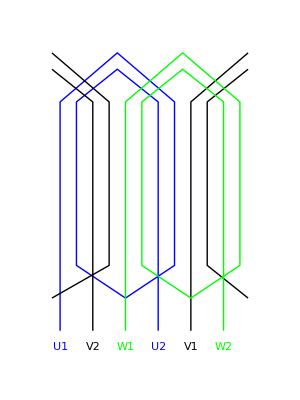

```mathematica
Graphics[{Blue,Thick,
circuit[],
Text[U1,{1,-5}],
Text[U2,{7,-5}],
Black,Thick,
Line[{
{9,-4},{9,10},
{12.5,13}
}],
Line[{
{12.5,-2},{10,0},
{10,10},{12.5,12}
}],
Line[{
{0.5,13},{4,10},
{4,0},{0.5,-2}
}],
Line[{
{0.5,12},{3,10},
{3,-4}
}],
Text[V2,{3,-5}],
Text[V1,{9,-5}],
Green,Thick,
circuit[4],
Text[W1,{5,-5}],
Text[W2,{11,-5}]
},PlotRange->{{-1,14},{-6,14}}]
```

U1: 	0°		V1:	120°		W1:	240°	
U2:	180°		V2:	300°		W2:	 60°

## Counterclockwise rotation

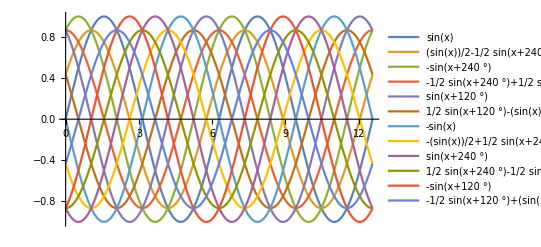

```mathematica
Plot[{Sin [x],Sin [x]/2-Sin [x+240Degree]/2 ,-Sin [x+240Degree],-Sin [x+240Degree]/2 + Sin [x+120Degree]/2, Sin [x+120Degree],Sin [x+120Degree]/2-Sin[x]/2,-Sin [x],-Sin[x]/2+Sin[x+240Degree]/2,Sin[x+240Degree],Sin[x+240Degree]/2-Sin[x+120Degree]/2,-Sin[x+120Degree],-Sin[x+120Degree]/2+Sin[x]/2}, {x,0,4Pi}, PlotLegends->"Expressions"]
```

```mathematica
Manipulate[Graphics[{Red,Thick,Line[{
{{1,0},{1,Sin[x]}},
{{2,0},{2,Sin [x]/2-Sin [x+240Degree]/2}},
{{3,0},{3,-Sin [x+240Degree]}},
{{4,0},{4,-Sin [x+240Degree]/2 + Sin [x+120Degree]/2}},
{{5,0},{5,Sin [x+120Degree]}},
{{6,0},{6,Sin [x+120Degree]/2-Sin[x]/2}},
{{7,0},{7,-Sin[x]}},
{{8,0},{8,-Sin[x]/2+Sin[x+240Degree]/2}},
{{9,0},{9,Sin[x+240Degree]}},
{{10,0},{10,Sin[x+240Degree]/2-Sin[x+120Degree]/2}},
{{11,0},{11,-Sin[x+120Degree]}},
{{12,0},{12,-Sin[x+120Degree]/2+Sin[x]/2}}
}]},Axes->True,GridLines->Automatic,PlotRange->{{-1,13},{-2,2}}],{x,0,8Pi}]
```

```mathematica
Manipulate[Graphics[{Red,Thick,Circle[{0,0},10],Blue,
Circle[{Sin[345Degree]*10,Cos[345Degree]*10},1],
Line[{{Sin[45Degree]*0.5+Sin[345Degree]*10,Cos[45Degree]*0.5+Cos[345Degree]*10},{Sin[45Degree]*-0.5+Sin[345Degree]*10,Cos[45Degree]*-0.5+Cos[345Degree]*10}}],
Line[{{Sin[45Degree]*0.5+Sin[345Degree]*10,Cos[45Degree]*-0.5+Cos[345Degree]*10},{Sin[45Degree]*-0.5+Sin[345Degree]*10,Cos[45Degree]*0.5+Cos[345Degree]*10}}],
Circle[{Sin[15Degree]*10,Cos[15Degree]*10},1],
Line[{{Sin[45Degree]*0.5+Sin[15Degree]*10,Cos[45Degree]*0.5+Cos[15Degree]*10},{Sin[45Degree]*-0.5+Sin[15Degree]*10,Cos[45Degree]*-0.5+Cos[15Degree]*10}}],
Line[{{Sin[45Degree]*0.5+Sin[15Degree]*10,Cos[45Degree]*-0.5+Cos[15Degree]*10},{Sin[45Degree]*-0.5+Sin[15Degree]*10,Cos[45Degree]*0.5+Cos[15Degree]*10}}],Black,
Circle[{Sin[45Degree]*10,Cos[45Degree]*10},1],
Disk[{Sin[45Degree]*10,Cos[45Degree]*10},0.5],
Circle[{Sin[75Degree]*10,Cos[75Degree]*10},1],
Disk[{Sin[75Degree]*10,Cos[75Degree]*10},0.5],Green,
Circle[{Sin[105Degree]*10,Cos[105Degree]*10},1],
Line[{{Sin[45Degree]*0.5+Sin[105Degree]*10,Cos[45Degree]*0.5+Cos[105Degree]*10},{Sin[45Degree]*-0.5+Sin[105Degree]*10,Cos[45Degree]*-0.5+Cos[105Degree]*10}}],
Line[{{Sin[45Degree]*0.5+Sin[105Degree]*10,Cos[45Degree]*-0.5+Cos[105Degree]*10},{Sin[45Degree]*-0.5+Sin[105Degree]*10,Cos[45Degree]*0.5+Cos[105Degree]*10}}],
Circle[{Sin[135Degree]*10,Cos[135Degree]*10},1],Line[{{Sin[45Degree]*0.5+Sin[135Degree]*10,Cos[45Degree]*0.5+Cos[135Degree]*10},{Sin[45Degree]*-0.5+Sin[135Degree]*10,Cos[45Degree]*-0.5+Cos[135Degree]*10}}],
Line[{{Sin[45Degree]*0.5+Sin[135Degree]*10,Cos[45Degree]*-0.5+Cos[135Degree]*10},{Sin[45Degree]*-0.5+Sin[135Degree]*10,Cos[45Degree]*0.5+Cos[135Degree]*10}}],Blue,
Circle[{Sin[165Degree]*10,Cos[165Degree]*10},1],
Disk[{Sin[165Degree]*10,Cos[165Degree]*10},0.5],
Circle[{Sin[195Degree]*10,Cos[195Degree]*10},1],
Disk[{Sin[195Degree]*10,Cos[195Degree]*10},0.5],Black,
Circle[{Sin[225Degree]*10,Cos[225Degree]*10},1],
Line[{{Sin[45Degree]*0.5+Sin[225Degree]*10,Cos[45Degree]*0.5+Cos[225Degree]*10},{Sin[45Degree]*-0.5+Sin[225Degree]*10,Cos[45Degree]*-0.5+Cos[225Degree]*10}}],
Line[{{Sin[45Degree]*0.5+Sin[225Degree]*10,Cos[45Degree]*-0.5+Cos[225Degree]*10},{Sin[45Degree]*-0.5+Sin[225Degree]*10,Cos[45Degree]*0.5+Cos[225Degree]*10}}],
Circle[{Sin[255Degree]*10,Cos[255Degree]*10},1],
Line[{{Sin[45Degree]*0.5+Sin[255Degree]*10,Cos[45Degree]*0.5+Cos[255Degree]*10},{Sin[45Degree]*-0.5+Sin[255Degree]*10,Cos[45Degree]*-0.5+Cos[255Degree]*10}}],
Line[{{Sin[45Degree]*0.5+Sin[255Degree]*10,Cos[45Degree]*-0.5+Cos[255Degree]*10},{Sin[45Degree]*-0.5+Sin[255Degree]*10,Cos[45Degree]*0.5+Cos[255Degree]*10}}],Green,
Circle[{Sin[285Degree]*10,Cos[285Degree]*10},1],
Disk[{Sin[285Degree]*10,Cos[285Degree]*10},0.5],
Circle[{Sin[315Degree]*10,Cos[315Degree]*10},1],
Disk[{Sin[315Degree]*10,Cos[315Degree]*10},0.5],Red,
Line[{
(*magnetic induction vectors*)
{{Sin[0Degree]*10,Cos[0Degree]*10},{Sin[0Degree]*10+Sin[0Degree]*(Sin[x]),Cos[0Degree]*10+Cos[0Degree]*(Sin[x])}},
{{Sin[30Degree]*10,Cos[30Degree]*10},{Sin[30Degree]*10+Sin[30Degree]*(Sin [x]/2-Sin [x+240Degree]/2),Cos[30Degree]*10+Cos[30Degree]*(Sin [x]/2-Sin [x+240Degree]/2)}},
{{Sin[60Degree]*10,Cos[60Degree]*10},{Sin[60Degree]*10+Sin[60Degree]*(-Sin [x+240Degree]),Cos[60Degree]*10+Cos[60Degree]*(-Sin [x+240Degree])}},
{{Sin[90Degree]*10,Cos[90Degree]*10},{Sin[90Degree]*10+Sin[90Degree]*(-Sin [x+240Degree]/2 + Sin [x+120Degree]/2),Cos[90Degree]*10+Cos[90Degree]*(-Sin [x+240Degree]/2 + Sin [x+120Degree]/2)}},
{{Sin[120Degree]*10,Cos[120Degree]*10},{Sin[120Degree]*10+Sin[120Degree]*(Sin [x+120Degree]),Cos[120Degree]*10+Cos[120Degree]*(Sin [x+120Degree])}},
{{Sin[150Degree]*10,Cos[150Degree]*10},{Sin[150Degree]*10 + Sin[150Degree]*(Sin [x+120Degree]/2-Sin[x]/2),Cos[150Degree]*10+Cos[150Degree]*(Sin [x+120Degree]/2-Sin[x]/2)}},
{{Sin[180Degree]*10,Cos[180Degree]*10},{Sin[180Degree]*10+Sin[180Degree]*(-Sin[x]),Cos[180Degree]*10+Cos[180Degree]*(-Sin[x])}},
{{Sin[210Degree]*10,Cos[210Degree]*10},{Sin[210Degree]*10+Sin[210Degree]*(-Sin[x]/2+Sin[x+240Degree]/2),Cos[210Degree]*10+Cos[210Degree]*(-Sin[x]/2+Sin[x+240Degree]/2)}},
{{Sin[240Degree]*10,Cos[240Degree]*10},{Sin[240Degree]*10+Sin[240Degree]*(Sin[x+240Degree]),Cos[240Degree]*10+Cos[240Degree]*(Sin[x+240Degree])}},
{{Sin[270Degree]*10,Cos[270Degree]*10},{Sin[270Degree]*10+Sin[270Degree]*(Sin[x+240Degree]/2-Sin[x+120Degree]/2),Cos[270Degree]*10+Cos[270Degree]*(Sin[x+240Degree]/2-Sin[x+120Degree]/2)}},
{{Sin[300Degree]*10,Cos[300Degree]*10},{Sin[300Degree]*10+Sin[300Degree]*(-Sin[x+120Degree]),Cos[300Degree]*10+Cos[300Degree]*(-Sin[x+120Degree])}},
{{Sin[330Degree]*10,Cos[330Degree]*10},{Sin[330Degree]*10+Sin[330Degree]*(-Sin[x+120Degree]/2+Sin[x]/2),Cos[330Degree]*10+Cos[330Degree]*(-Sin[x+120Degree]/2+Sin[x]/2)}},
(*rotating magnetic induction vector*)
{{0,0},
{Sin[0Degree]*(Sin[x])+
Sin[30Degree]*(Sin [x]/2-Sin [x+240Degree]/2)+
Sin[60Degree]*(-Sin[x+240Degree])+
Sin[90Degree]*(-Sin [x+240Degree]/2 + Sin [x+120Degree]/2)+
Sin[120Degree]*(Sin [x+120Degree])+
Sin[150Degree]*(Sin [x+120Degree]/2-Sin[x]/2)+
Sin[180Degree]*(-Sin[x])+
Sin[210Degree]*(-Sin[x]/2+Sin[x+240Degree]/2)+
Sin[240Degree]*(Sin[x+240Degree])+
Sin[270Degree]*(Sin[x+240Degree]/2-Sin[x+120Degree]/2)+
Sin[300Degree]*(-Sin[x+120Degree])+
Sin[330Degree]*(-Sin[x+120Degree]/2+Sin[x]/2),
Cos[0Degree]*(Sin[x])+
Cos[30Degree]*(Sin [x]/2-Sin [x+240Degree]/2)+
Cos[60Degree]*(-Sin[x+240Degree])+
Cos[90Degree]*(-Sin [x+240Degree]/2 + Sin [x+120Degree]/2)+
Cos[120Degree]*(Sin [x+120Degree])+
Cos[150Degree]*(Sin [x+120Degree]/2-Sin[x]/2)+
Cos[180Degree]*(-Sin[x])+
Cos[210Degree]*(-Sin[x]/2+Sin[x+240Degree]/2)+
Cos[240Degree]*(Sin[x+240Degree])+
Cos[270Degree]*(Sin[x+240Degree]/2-Sin[x+120Degree]/2)+
Cos[300Degree]*(-Sin[x+120Degree])+
Cos[330Degree]*(-Sin[x+120Degree]/2+Sin[x]/2)}}
}]},Axes->True,GridLines->Automatic,PlotRange->{{-11,11},{-11,11}}],{x,0,8Pi}]
```

U1: 	0°		V1:	120°		W1:	240°	
U2:	180°		V2:	 300°		W2:	 60°

## Wiring diagram

```mathematica
circuit[x_:0]:=Line[{
{1+x,-4},{1+x,10},
{4.5+x,13},{8+x,10},{8+x,0},
{5+x,-2},{2+x,0},
{2+x,10},{4.5+x,12},
{7+x,10},{7+x,-4}
}]
```

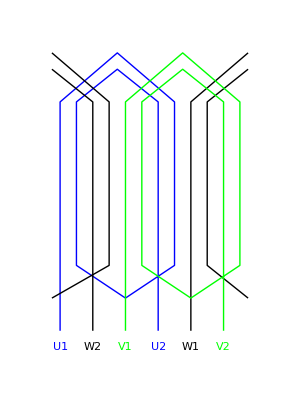

```mathematica
Graphics[{Blue,Thick,
circuit[],
Text[U1,{1,-5}],
Text[U2,{7,-5}],
Black,Thick,
Line[{
{9,-4},{9,10},
{12.5,13}
}],
Line[{
{12.5,-2},{10,0},
{10,10},{12.5,12}
}],
Line[{
{0.5,13},{4,10},
{4,0},{0.5,-2}
}],
Line[{
{0.5,12},{3,10},
{3,-4}
}],
Text[W2,{3,-5}],
Text[W1,{9,-5}],
Green,Thick,
circuit[4],
Text[V1,{5,-5}],
Text[V2,{11,-5}]
},PlotRange->{{-1,14},{-6,14}}]
```

U1: 	0°		V1:	120°		W1:	240°	
U2:	180°		V2:	 300°		W2:	 60°

General::prng: Value of option PlotRange -> {«1»} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.